## Functions

```mathematica
(*rotation matrix*)
Rz[α_]:={{Cos[α],-Sin[α]},{Sin[α],Cos[α]}};
```

## Variables

```mathematica
(*configuration space*)
q={θ1,θ2,θ3,ϕ1,ϕ2,ϕ3,x,y,α};
(* Active variables *)
θ = {θ1,θ2,θ3};
(* Passive variables *)
ϕ = {ϕ1,ϕ2,ϕ3,x,y,α};
(* Task Space *)
ψ={x,y,α};
(*substitute variables as functions of time*)
subsqt={
θ1-> θ1[t],θ2-> θ2[t],θ3-> θ3[t],
ϕ1-> ϕ1[t],ϕ2-> ϕ2[t],ϕ3-> ϕ3[t],
x-> x[t],y-> y[t],α-> α[t]};
qt=q/.subsqt;
```

## Coordinates of vertices of the end effectors, p_i

```mathematica
b1 = {0,0};
b2 = {√3 b,0}; 
b3={(√3)/2 b,3/2 b};
```

```mathematica
(*expressed interms of joint space variables*)
p1a=b1+ lcr*{Cos[θ1],Sin[θ1]}+lst*{Cos[ϕ1],Sin[ϕ1]};
p2a=b2+ lcr*{Cos[θ2],Sin[θ2]}+lst*{Cos[ϕ2],Sin[ϕ2]};
p3a=b3+ lcr*{Cos[θ3],Sin[θ3]}+lst*{Cos[ϕ3],Sin[ϕ3]};
pca=(p1+p2+p3)/3;
```

```mathematica
(*expressed interms of taskspace variables*)
pcb={x,y};
p1b = Simplify[TrigExpand[pcb + Rz[210 π/180+α].{a,0}]];
p2b = Simplify[TrigExpand[pcb+ Rz[-30 π/180+α].{a,0}]];
p3b = Simplify[TrigExpand[pcb + Rz[90 π/180+α].{a,0}]];
```

## Mass centers and velocity Jacobians

```mathematica
(*position of center of mass of the cranks*)
pCr1=b1+ lcr/2*{Cos[θ1],Sin[θ1]};
pCr2=b2+ lcr/2*{Cos[θ2],Sin[θ2]};
pCr3=b3+ lcr/2*{Cos[θ3],Sin[θ3]};
(*linear velocity jacobian for crank C.O.M.*)
JvCr1=D[pCr1,{q}];
JvCr2=D[pCr2,{q}];
JvCr3=D[pCr3,{q}];

(*position of center of mass of strut*)
pSt1=b1+ lcr*{Cos[θ1],Sin[θ1]}+lst/2*{Cos[ϕ1],Sin[ϕ1]};
pSt2=b2+ lcr*{Cos[θ2],Sin[θ2]}+lst/2*{Cos[ϕ2],Sin[ϕ2]};
pSt3=b3+ lcr*{Cos[θ3],Sin[θ3]}+lst/2*{Cos[ϕ3],Sin[ϕ3]};
(*linear velocity jacobian for strut C.O.M.*)
JvSt1=D[pSt1,{q}];
JvSt2=D[pSt2,{q}];
JvSt3=D[pSt3,{q}];

(*linear velocity jacobian for endeffector*)
JvEe=D[pcb,{q}];

(*co-ordinates of payload 1: *)
pPl=pcb + Rz[α].{xPl,yPl};

(*linear velocity jacobian for centroid of end effector and payload C.O.M.*)
JvPl=D[pPl,{q}];

θCr1={0,0,θ1};
θCr2={0,0,θ2};
θCr3={0,0,θ3};

(*angular velocity jacobian for crank angles*)
JωCr1=D[θCr1,{q}];
JωCr2=D[θCr2,{q}];
JωCr3=D[θCr3,{q}];

θSt1={0,0,ϕ1};
θSt2={0,0,ϕ2};
θSt3={0,0,ϕ3};

(*angular velocity jacobian for passive link's angles*)
JωSt1=D[θSt1,{q}];
JωSt2=D[θSt2,{q}];
JωSt3=D[θSt3,{q}];

θEe={0,0,α};
(*angular velocity jacobian for end effector's and payload's angle*)
JωEe=D[θEe,{q}];
```

## Mass matrices

```mathematica
(*mass moment of inertia matrices*)
ICr={{0,0,0},{0,0,0},{0,0,ICrz}};
ISt={{0,0,0},{0,0,0},{0,0,IStz}};
IEe={{0,0,0},{0,0,0},{0,0,ITpz}};
IPl={{0,0,0},{0,0,0},{0,0,IPlz}};
(*Mass matrices*)
Mleg1=TrigExpand[Simplify[mCr*Transpose[JvCr1].JvCr1+Transpose[JωCr1].ICr.JωCr1+mSt*Transpose[JvSt1].JvSt1+Transpose[JωSt1].ISt.JωSt1]];
Mleg2=TrigExpand[Simplify[mCr*Transpose[JvCr2].JvCr2+Transpose[JωCr2].ICr.JωCr2+mSt*Transpose[JvSt2].JvSt2+Transpose[JωSt2].ISt.JωSt2]];
Mleg3=TrigExpand[Simplify[mCr*Transpose[JvCr3].JvCr3+Transpose[JωCr3].ICr.JωCr3+  mSt*Transpose[JvSt3].JvSt3+Transpose[JωSt3].ISt.JωSt3]];
MEe=TrigExpand[Simplify[mEe*Transpose[JvEe].JvEe+Transpose[JωEe].IEe.JωEe]];
MPl=TrigExpand[Simplify[mPl*Transpose[JvPl].JvPl+Transpose[JωEe].IPl.JωEe]];
(*mass matrix for the manipulator*)
Mq3RRR=Simplify[Mleg1+Mleg2+Mleg3+MEe+MPl];
```

## C matrix

```mathematica
(*computation of C matrix *)
CmfromM[massMatrix_,q_]:=Module[{n,dMdq,count,ii,jj,kk,querydMdq,cmat},
n=Length[q];
dMdq=ConstantArray[0,{n*(n+1)/2,n}];
count=1;
For[ii=1,ii≤n,ii++,For[jj=1,jj≤ii,jj++,dMdq[[count]]=D[massMatrix[[ii,jj]],{q}];
count++;];];
querydMdq[ii_,jj_,kk_]:=If[ii>jj,Return[dMdq[[(ii-1)*ii/2+jj,kk]]];,Return[dMdq[[(jj-1)*jj/2+ii,kk]]];];
cmat=ConstantArray[0,{n,n}];
For[ii=1,ii≤n,ii++,For[jj=1,jj≤n,jj++,For[kk=1,kk≤n,kk++,cmat[[ii,jj]]+=(querydMdq[ii,jj,kk]+querydMdq[ii,kk,jj]-querydMdq[kk,jj,ii])*D[q[[kk]],t];];];];
cmat=1/2*cmat;
Return[cmat];];

Cq3RRRt=CmfromM[Mq3RRR/.subsqt,qt];
Mq3RRR/.subsqt;
```

## RR-dyad function

```mathematica
rrdyad[{l1_,l2_,{x0_,y0_},{x1_,y1_},θ1_,θ2_}]:= Module[{t1,t2,a0,a1,a2,d1,ϕ,θd,solθ1,solθ2,solθ},
t1 = x0-x1;
t2 = y0-y1;
a0 = -l1^2+l2^2+t1^2+t2^2;
a1=2 *l2*t1 ;
a2=2 *l2 *t2;
d1 = Sqrt[a1^2+a2^2];
ϕ = ArcTan[a1,a2];
θd = ArcCos[-a0/d1];
solθ2 = {{θ2-> ϕ+θd},{θ2-> ϕ-θd}};
solθ1 = {θ1-> ArcTan[-t1-l2*Cos[θ2],-t2-l2*Sin[θ2]]}/.solθ2;
solθ =N[ Join[solθ1,solθ2,2]];

Return[solθ];
];
```

## Inverse Kinematics

```mathematica
IK3RRR[ψ_,θ_,ϕ_,{b_,l_,r_,a_},branch_:2]:=Module[{xc,yc,α,θ1,θ2,θ3,ϕ1,ϕ2,ϕ3,R,p1,p2,p3,b1,b2,b3,solxy1,solxy2,solxy3,solθ1,solθ2,solθ3,solϕ1,solϕ2,solϕ3,x,y,sol},
{xc,yc,α}=ψ;
{θ1,θ2,θ3}=θ;
{ϕ1,ϕ2,ϕ3}=ϕ;

R={{Cos[α],-Sin[α]},{Sin[α],Cos[α]}};

(* Top Platform vertices *)
p1={xc,yc}+a*R.{Cos[-5π/6],Sin[-5π/6]};
p2={xc,yc}+a*R.{Cos[-π/6],Sin[-π/6]};
p3={xc,yc}+a*R.{Cos[π/2],Sin[π/2]};

(* Base Platform Vertices *)
b1={0,0};
b2={b*√3,0};
b3=b*{√3/2,3/2};

(* Solve the θ and ϕ for leg 1 *)
sol1=rrdyad[{lcr,lst,b1,p1,θ1,ϕ1}/.data][[2]];
(* Solve the θ and ϕ for leg 2 *)
sol2=rrdyad[{lcr,lst,b2,p2,θ2,ϕ2}/.data][[2]];
(* Solve the θ and ϕ for leg 1 *)
sol3=rrdyad[{lcr,lst,b3,p3,θ3,ϕ3}/.data][[2]];

(*Combined solution*)
sol=Join[sol1,sol2,sol3];

Return[sol];
];
```

## 1^st order and 2^nd order inverse inverse kinematics

```mathematica
(*joint variables*)
β={θ1,θ2,θ3,ϕ1,ϕ2,ϕ3};
βt=β/.subsqt;

(*task space variables*)
X= {x,y,α};
Xt=X/.subsqt;
dX=D[Xt,t];
ddX=D[Xt,{t,2}];

ηik1=(p1a -p1b)[[1]];
ηik2=(p1a -p1b)[[2]];
ηik3=(p2a -p2b)[[1]];
ηik4=(p2a -p2b)[[2]];
ηik5=(p3a -p3b)[[1]];
ηik6=(p3a -p3b)[[2]];

ηik = {ηik1,ηik2,ηik3,ηik4,ηik5,ηik6};

(*required matrices*)
Jηβ =Simplify[D[ηik,{β}]];
Jηx =Simplify[D[ηik,{X}]];

Jηβt=Jηβ/.subsqt;
Jηxt=Jηx/.subsqt;

Jβxt=-Inverse[Jηβt].Jηxt;
Jβxdot=D[Jβxt,t];

Jηβtdot = D[Jηβt , t];
Jηxtdot = D[Jηxt , t];

Jηθ=D[ηik,{θ}];
Jηϕ=D[ηik,{ϕ}]//Simplify;

Jϕθ=-Inverse[Jηϕ].Jηθ//Simplify;
```

## Equation of motion

```mathematica
θt=θ/.subsqt;
dθt=D[θt,t];
ddθt=D[θt,{t,2}];

Jqθ=Join[IdentityMatrix[3],Jϕθ]/.subsqt;
Jqθdot=D[Jqθ,t]//Simplify;

(* Writing the mass matrix in the actuator space *)
Mq3RRRt=Mq3RRR/.subsqt;
Mθ=Transpose[Jqθ].Mq3RRRt.Jqθ;
Cθ=Transpose[Jqθ].Cq3RRRt.Jqθ + Transpose[Jqθ].Mq3RRRt.Jqθdot;
```

## Defining Circular paths

```mathematica
(*Data*)

(*Design 1*)
massdata={mCr->1.536,mSt->1.163,mEe->0.113,mPl->1.5,ICrz->0.0374,IStz->0.0242,ITpz->0,xPl->0,yPl->0,IPlz->1};
lendata={b->0.462,lcr->0.402,lst->0.500,a->0.162,αmid->139};

(*Design 2*)
(*massdata={mCr->1.505,mSt->1.121,mEe->0.105,mPl->1.5,ICrz->0.035,IStz->0.022,ITpz->0,xPl->0,yPl->0,IPlz->1};
lendata={b->0.455,lcr->0.397,lst->0.491,a->0.151,αmid->140};*)

(*Design 3*)
(*massdata={mCr->2.04,mSt->1.16,mEe->0.168,mPl->1.5,ICrz->0.066,IStz->0.024,ITpz->0,xPl->0,yPl->0,IPlz->1};
lendata={b->0.540,lcr->0.478,lst->0.5,a->0.24,αmid->110};*)

(*Existing Design*)
(*massdata={mCr->2.69,mSt->1.56,mEe->0.06,mPl->1.5,ICrz->0.077,IStz->0.024,ITpz->0,xPl->0,yPl->0,IPlz->1};
lendata={b->0.578,lcr->0.5,lst->0.5,a->0.086,αmid->68};*)

data=Flatten[{massdata,lendata,γdot->9.5,rad->0.03}];
```

## Inverse kinematics substitution

```mathematica
pos=b*{Cos[π/6],Sin[π/6]}+{x0,y0}+rad*{Cos[γ[tim]],Sin[γ[tim]]};
vel=D[pos,{tim}];
acc=D[pos,{tim,2}];

(* The end effector goes around the circular trajectory at constant speed *)
possub={γ[tim]->tim*γdot};
velaccsub=Inner[Rule,{γ'[tim],γ''[tim]},{γdot,0},List];

subpos=Inner[Rule,Xt,Join[pos/.possub/.data,{0}],List];
subvel=Inner[Rule,dX,Join[vel/.velaccsub/.possub/.data,{0}],List];
subacc=Inner[Rule,ddX,Join[acc/.velaccsub/.possub/.data,{0}],List];
eqmotion=(Mθ.ddθt+Cθ.dθt)/.data;
```

## Torque calculation function

```mathematica
func[test_,{xx_,yy_}]:=Module[{},
tsub={tim->test,x0->xx,y0->yy};
iksol=IK3RRR[Xt/.subpos/.tsub,θ/.subsqt,{ϕ1,ϕ2,ϕ3}/.subsqt,{b,lcr,lst,a}/.data];
fullconfig=Join[subpos,iksol]/.data/.tsub;
dβsub=θdotsub=Inner[Rule,D[β/.subsqt,t],Jβxt.dX/.subvel/.fullconfig/.data,List]/.tsub;
fullconfigvel=Join[subvel,dβsub]/.data/.tsub;
ddβsub=Inner[Rule,D[β/.subsqt,{t,2}],(Jβxt.ddX+Jβxdot.dX)/.subacc/.subvel/.subpos/.fullconfig/.θdotsub/.data,List]/.tsub;
Return[eqmotion/.fullconfig/.fullconfigvel/.ddβsub];]
```

## Plotting torque

```mathematica
rd=0.1;
p0={0,0};
p1={rd,0};
p2={0,rd};
p3={-rd,0};
p4={0,-rd};
p5={2*rd,0};
p6={0,2*rd};
p7={-2*rd,0};
p8={0,-2*rd};

(*val0=Table[{temp,func[temp,p0][[1]]},{temp,0,2π/8.75,0.02}];*)
val1=Table[{temp*(γdot/.data)*180/π,func[temp,p1][[1]]},{temp,0,2π/(γdot/.data),0.01}];
(*val2=Table[{temp,func[temp,p2][[1]]},{temp,0,2π/8.75,0.02}];*)
val3=Table[{temp*(γdot/.data)*180/π,func[temp,p3][[1]]},{temp,0,2π/(γdot/.data),0.01}];
(*val4=Table[{temp,func[temp,p4][[1]]},{temp,0,2π/8.75,0.02}];*)
val5=Table[{temp*(γdot/.data)*180/π,func[temp,p5][[1]]},{temp,0,2π/(γdot/.data),0.01}];
(*val6=Table[{temp,func[temp,p6][[1]]},{temp,0,2π/8.75,0.02}];*)
val7=Table[{temp*(γdot/.data)*180/π,func[temp,p7][[1]]},{temp,0,2π/(γdot/.data),0.01}];
(*val8=Table[{temp,func[temp,p8][[1]]},{temp,0,2π/8.75,0.02}];*)
```

```mathematica
ModelAtest1=val1;
ModelAtest2=val3;
ModelAtest3=val5;
ModelAtest4=val7;
```

```mathematica
ModelBtest1=val1;
ModelBtest2=val3;
ModelBtest3=val5;
ModelBtest4=val7;
```

```mathematica
ModelCtest1=val1;
ModelCtest2=val3;
ModelCtest3=val5;
ModelCtest4=val7;
```

```mathematica
ModelDtest1=val1;
ModelDtest2=val3;
ModelDtest3=val5;
ModelDtest4=val7;
```

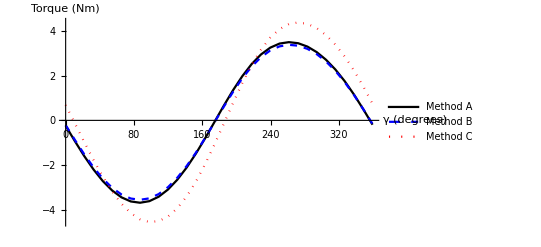

```mathematica
plot1=ListLinePlot[{ModelAtest1,ModelBtest1,ModelCtest1},PlotStyle->{Black, Directive[Blue,Dashed],Directive[Red,Dotted]},PlotLegends->{"Method A", "Method B", "Method C"},AxesLabel->{"γ (degrees)", "Torque (Nm)"},AxesStyle->Directive[Black,Bold,12],LabelStyle->(FontFamily->"CMU Serif"),PlotRange->Automatic]
```

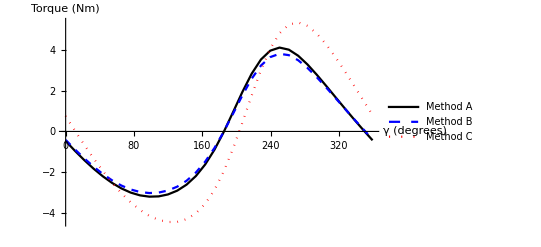

```mathematica
plot2=ListLinePlot[{ModelAtest2,ModelBtest2,ModelCtest2},PlotStyle->{Black, Directive[Blue,Dashed],Directive[Red,Dotted]},PlotLegends->{"Method A", "Method B", "Method C"},AxesLabel->{"γ (degrees)", "Torque (Nm)"},AxesStyle->Directive[Black,Bold,12],LabelStyle->(FontFamily->"CMU Serif"),PlotRange->Automatic]
```

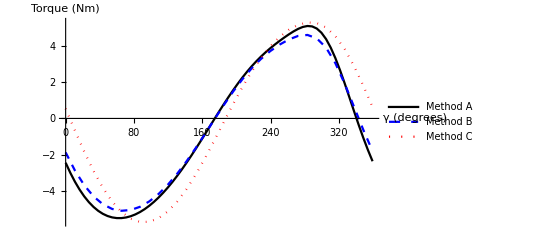

```mathematica
plot3=ListLinePlot[{ModelAtest3,ModelBtest3,ModelCtest3},PlotStyle->{Black, Directive[Blue,Dashed],Directive[Red,Dotted]},PlotLegends->{"Method A", "Method B", "Method C"},AxesLabel->{"γ (degrees)", "Torque (Nm)"},AxesStyle->Directive[Black,Bold,12],LabelStyle->(FontFamily->"CMU Serif"),PlotRange->Automatic]
```

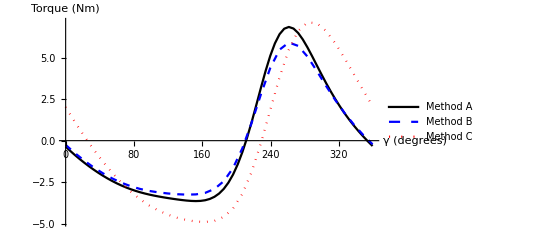

```mathematica
plot4=ListLinePlot[{ModelAtest4,ModelBtest4,ModelCtest4},PlotStyle->{Black, Directive[Blue,Dashed],Directive[Red,Dotted]},PlotLegends->{"Method A", "Method B", "Method C","Existing Design"},AxesLabel->{"γ (degrees)", "Torque (Nm)"},AxesStyle->Directive[Black,Bold,12],LabelStyle->(FontFamily->"CMU Serif"),PlotRange->Automatic]
```

```mathematica
Export["3rrrTest1.pdf",plot1];
Export["3rrrTest2.pdf",plot2];
Export["3rrrTest3.pdf",plot3];
Export["3rrrTest4.pdf",plot4];
```